# Annotated code and results for “Fully Automated Cancer Diagnosis through a Tandem of Classifiers for Digitized Histopathological Slides”

## Code to create the test sets and classifier functions

### Start with FCT+PCA method

To access the images one can go to 
https://storage.rcs-rds.ro/links/888ccd47-f84e-4510-b4dc-865cf69bca16
which may also be also found via
https://sites.google.com/site/imediatreat/data-sets
Hitting the “Save” button gives a zipped directory. I unzipped in a subdirectory of my home directory, named “histology_images” (no quotes, since I am on a Linux desktop). The images can now be imported to Mathematica as below.

```mathematica
AbsoluteTiming[GImages=FileSystemMap[Import[#,"JPG"]&,FileNameJoin[{$HomeDirectory,"histology_images"}],{2}];]
GImages=Map[Values,Values[GImages]];
```

{18.3833,Null}

```mathematica
Map[Length,GImages]
```

{62,96,99,100}

We set up some lists for the test values (the images will change with random sampling, but not these values since we take the same amount from each of the four classes of image).

```mathematica
testValueLens=Map[Round[Length[#]*1/3]&,GImages]
testValues=Apply[Join,MapIndexed[ConstantArray[#2[[1]]-1,#1]&,testValueLens]]
```

{21,32,33,33}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}

Below are some parameters found to give good results for this method. We also preprocess by taking Fourier cosine transforms of all images and retaining only the low frequency square of components that was found to work best (4x4, in this case).

```mathematica
keep=4;
dn=4;
dct=2;
GImagesS=GImages;
```

```mathematica
AbsoluteTiming[dctvecs=Table[Flatten[FourierDCT[ImageData[GImagesS[[j,k]]]][[1;;dn,1;;dn]]],
{j,Length[GImages]},{k,Length[GImages[[j]]]}];]
```

{33.7514,Null}

```mathematica
nearestImages[dctvecs_,vals_,keep_]:=Module[{uu,ww,vv,udotw,norms},
{uu,ww,vv}=SingularValueDecomposition[dctvecs,keep];udotw=uu.ww;norms=(√(#1.#1)&)/@udotw;udotw=udotw/norms;
{Nearest[udotw->Transpose[{udotw,vals}]],vv}]

processInput[dctvecs_,vv_]:=
Module[
{tdotv,norms},
tdotv=dctvecs.vv;
norms=Map[Sqrt[#.#]&,tdotv];
tdotv=tdotv/norms;
tdotv]
```

We use weights inversely proportional to distances between test vectors and neighbor vectors. This emulates “probabilities” of correct guesses.

```mathematica
guesses[nf_,tvecs_,n_]:=Module[
{nbrs,probs,probsB,bestvals},
probs=Table[
Module[{res=nf[tvecs[[j]],n],dists},
dists=1/Map[Norm[tvecs[[j]]-#]&,res[[All,1]]];
Thread[{res[[All,2]],dists/Total[dists]}]],
{j,Length[tvecs]}];
probsB=Map[Normal[GroupBy[#,First]]&,probs]/.(val_->vlist:{{val_,_}..}):>(val->Total[vlist[[All,2]]]);
probs=({0,1,2,3}/.probsB)/.Thread[{0,1,2,3}->0];
bestvals=Map[First[Ordering[#,1,Greater]-1]&,probs,{1}];
bestvals
]

correct[guess_,actual_]/;
Length[guess]==Length[actual]:=
Count[guess-actual,0]
correct[__]:=$Failed
```

```mathematica
runRecognitionTest[imageSets_,fraction_,repeat_,n_]:=Module[
{testSets,trainingSets,results,allTrainingImages,allTestImages,trainingValues,testValues,nfunc,vv,testvecs,guessed},
results=Table[
testSets=Map[RandomSample[#,Round[Length[#]*fraction]]&,imageSets];
trainingSets=Apply[Complement,Transpose[{imageSets,testSets}],{1}];
allTrainingImages=Apply[Join,trainingSets];
allTestImages=Apply[Join,testSets];
trainingValues=Apply[Join,MapIndexed[ConstantArray[#2[[1]]-1,Length[#1]]&,trainingSets]];
testValues=Apply[Join,MapIndexed[ConstantArray[#2[[1]]-1,Length[#1]]&,testSets]];
{nfunc,vv}=
nearestImages[allTrainingImages,trainingValues,keep];
testvecs=processInput[allTestImages,vv];
guessed=guesses[nfunc,testvecs,n];
Clear[nfunc,vv,testvecs,allTrainingImages,allTestImages];
correct[guessed,testValues]
,{j,repeat}];
{results,Mean[N@results]/Length[Apply[Join,testSets]]}
]
```

We check how well the FCT+PCA method works on 100 runs. Each uses a random sample size, from the four categories, of 2/3 for training and 1/3 for testing.

```mathematica
SeedRandom[11111];
AbsoluteTiming[runRecognitionTest[dctvecs,1/3,100,4]]
```

{0.644893,{{107,110,104,109,107,107,104,104,108,111,110,104,110,107,113,106,106,107,110,106,103,110,108,111,106,103,104,107,108,108,106,105,113,105,107,102,110,109,108,103,106,101,106,104,108,106,110,108,109,103,102,105,107,106,106,110,109,103,109,108,107,107,103,100,109,107,112,107,109,106,105,110,107,103,108,105,109,107,104,113,108,110,105,108,110,108,107,104,110,115,104,106,106,109,110,104,114,110,109,107},0.900336}}

So overall we are getting around 90% correct.

### This is the code to create 40 trials, using random samples of 2/3 training and 1/3 testing from each of the four categories

We weight the FCT+PCA neighbors by their reciprocal distances from the input, rather than using fixed weights for the four closest. It was also tried with varying powers of those reciprocal weights but this seems to work as well as any such variant well.

```mathematica
SeedRandom[11112222];
AbsoluteTiming[
allVals=Table[
Print[k];
testSetIndices=Map[RandomSample[Range[Length[#]],Round[Length[#]*1/3]]&,GImages];
testSets=Table[GImages[[j,testSetIndices[[j]]]],{j,Length[testSetIndices]}];
trainingSets=Apply[Complement,Transpose[{GImages,testSets}],{1}];
allTrainingImages=Apply[Join,trainingSets];
allTestImages=Apply[Join,testSets];trainingValues=Apply[Join,MapIndexed[ConstantArray[#2[[1]]-1,Length[#1]]&,trainingSets]];
testValues=Apply[Join,MapIndexed[ConstantArray[#2[[1]]-1,Length[#1]]&,testSets]];
methods={"RandomForest","NearestNeighbors","SupportVectorMachine","LogisticRegression","NeuralNetwork","NaiveBayes"};
cfuncs=Map[(Print[#];Print[AbsoluteTiming[cf=Classify[allTrainingImages->trainingValues, Method->#,PerformanceGoal->"Quality"];]];cf)&,methods];
resultprobsraw=({0,1,2,3}/.Table[Map[cfuncs[[j]][#,"Probabilities"]&,allTestImages],{j,Length[cfuncs]}]);
mlmethods[k]=resultprobsraw;
testDCTs=Table[dctvecs[[j,testSetIndices[[j]]]],{j,Length[testSetIndices]}];
trainingDCTs=Apply[Complement,Transpose[{dctvecs,testDCTs}],{1}];
allTrainingDCTs=Apply[Join,trainingDCTs];
allTestDCTs=Apply[Join,testDCTs];
{nfunc,vv}=
nearestImages[allTrainingDCTs,trainingValues,keep];
testvecs=processInput[allTestDCTs,vv];
nfuncresult=Table[
Module[{res=nfunc[testvecs[[j]],4],dists},
dists=1/Map[Norm[testvecs[[j]]-#]&,res[[All,1]]];
Thread[{res[[All,2]],dists/Total[dists]}]],
{j,Length[testvecs]}];
nfuncresultB=Map[Normal[GroupBy[#,First]]&,nfuncresult]/.(val_->vlist:{{val_,_}..}):>(val->Total[vlist[[All,2]]]);
nfuncprobs=({0,1,2,3}/.nfuncresultB)/.Thread[{0,1,2,3}->0];
fctpcaraw[k]=nfuncprobs;
Join[resultprobsraw,{nfuncprobs}]
,{k,40}];
]
```

1

RandomForest

{38.868,Null}

NearestNeighbors

{38.3891,Null}

SupportVectorMachine

{45.4457,Null}

LogisticRegression

{38.6423,Null}

NeuralNetwork

{121.112,Null}

NaiveBayes

{37.8518,Null}

2

RandomForest

{38.5812,Null}

NearestNeighbors

{37.7195,Null}

SupportVectorMachine

{44.2825,Null}

LogisticRegression

{37.9285,Null}

NeuralNetwork

{105.51,Null}

NaiveBayes

{38.1559,Null}

3

RandomForest

{39.3242,Null}

NearestNeighbors

{38.3367,Null}

SupportVectorMachine

{44.6268,Null}

LogisticRegression

{38.5928,Null}

NeuralNetwork

{111.551,Null}

NaiveBayes

{39.5485,Null}

4

RandomForest

{39.2007,Null}

NearestNeighbors

{38.2441,Null}

SupportVectorMachine

{44.1289,Null}

LogisticRegression

{38.1958,Null}

NeuralNetwork

{84.0532,Null}

NaiveBayes

{38.0812,Null}

5

RandomForest

{39.2242,Null}

NearestNeighbors

{38.468,Null}

SupportVectorMachine

{44.8886,Null}

LogisticRegression

{38.3601,Null}

NeuralNetwork

{83.8248,Null}

NaiveBayes

{38.303,Null}

6

RandomForest

{38.695,Null}

NearestNeighbors

{38.0606,Null}

SupportVectorMachine

{44.3967,Null}

LogisticRegression

{38.4408,Null}

NeuralNetwork

{154.502,Null}

NaiveBayes

{38.0221,Null}

7

RandomForest

{38.5942,Null}

NearestNeighbors

{38.3392,Null}

SupportVectorMachine

{43.9006,Null}

LogisticRegression

{38.1194,Null}

NeuralNetwork

{136.203,Null}

NaiveBayes

{37.8537,Null}

8

RandomForest

{39.1798,Null}

NearestNeighbors

{38.4153,Null}

SupportVectorMachine

{44.456,Null}

LogisticRegression

{38.8514,Null}

NeuralNetwork

{109.355,Null}

NaiveBayes

{37.8947,Null}

9

RandomForest

{39.0702,Null}

NearestNeighbors

{38.139,Null}

SupportVectorMachine

{44.8083,Null}

LogisticRegression

{38.2228,Null}

NeuralNetwork

{157.182,Null}

NaiveBayes

{38.1769,Null}

10

RandomForest

{38.6154,Null}

NearestNeighbors

{38.2597,Null}

SupportVectorMachine

{44.4997,Null}

LogisticRegression

{38.1857,Null}

NeuralNetwork

{84.8222,Null}

NaiveBayes

{38.2738,Null}

11

RandomForest

{38.5403,Null}

NearestNeighbors

{37.828,Null}

SupportVectorMachine

{45.0303,Null}

LogisticRegression

{38.2996,Null}

NeuralNetwork

{156.494,Null}

NaiveBayes

{38.3151,Null}

12

RandomForest

{38.9186,Null}

NearestNeighbors

{38.3019,Null}

SupportVectorMachine

{44.428,Null}

LogisticRegression

{38.6264,Null}

NeuralNetwork

{136.79,Null}

NaiveBayes

{38.2032,Null}

13

RandomForest

{38.5742,Null}

NearestNeighbors

{38.8569,Null}

SupportVectorMachine

{44.849,Null}

LogisticRegression

{38.73,Null}

NeuralNetwork

{84.1108,Null}

NaiveBayes

{37.9209,Null}

14

RandomForest

{39.1837,Null}

NearestNeighbors

{38.2375,Null}

SupportVectorMachine

{45.0042,Null}

LogisticRegression

{38.4813,Null}

NeuralNetwork

{95.3201,Null}

NaiveBayes

{38.4047,Null}

15

RandomForest

{38.7856,Null}

NearestNeighbors

{38.1201,Null}

SupportVectorMachine

{44.5061,Null}

LogisticRegression

{38.552,Null}

NeuralNetwork

{83.219,Null}

NaiveBayes

{38.0553,Null}

16

RandomForest

{38.4806,Null}

NearestNeighbors

{38.1292,Null}

SupportVectorMachine

{44.6789,Null}

LogisticRegression

{38.2728,Null}

NeuralNetwork

{94.7785,Null}

NaiveBayes

{37.8728,Null}

17

RandomForest

{38.4008,Null}

NearestNeighbors

{37.9911,Null}

SupportVectorMachine

{44.4002,Null}

LogisticRegression

{38.0909,Null}

NeuralNetwork

{94.06,Null}

NaiveBayes

{37.8228,Null}

18

RandomForest

{38.364,Null}

NearestNeighbors

{37.9644,Null}

SupportVectorMachine

{44.6647,Null}

LogisticRegression

{38.0168,Null}

NeuralNetwork

{83.0926,Null}

NaiveBayes

{37.8606,Null}

19

RandomForest

{38.3759,Null}

NearestNeighbors

{37.8693,Null}

SupportVectorMachine

{44.4185,Null}

LogisticRegression

{38.0212,Null}

NeuralNetwork

{146.16,Null}

NaiveBayes

{37.7904,Null}

20

RandomForest

{38.4852,Null}

NearestNeighbors

{37.7134,Null}

SupportVectorMachine

{44.4186,Null}

LogisticRegression

{38.1419,Null}

NeuralNetwork

{83.5435,Null}

NaiveBayes

{38.4178,Null}

21

RandomForest

{38.7292,Null}

NearestNeighbors

{38.2409,Null}

SupportVectorMachine

{44.3538,Null}

LogisticRegression

{38.633,Null}

NeuralNetwork

{83.489,Null}

NaiveBayes

{37.8139,Null}

22

RandomForest

{38.4646,Null}

NearestNeighbors

{37.7545,Null}

SupportVectorMachine

{44.0404,Null}

LogisticRegression

{37.983,Null}

NeuralNetwork

{94.3066,Null}

NaiveBayes

{37.8299,Null}

23

RandomForest

{38.4134,Null}

NearestNeighbors

{37.8133,Null}

SupportVectorMachine

{44.5786,Null}

LogisticRegression

{37.9771,Null}

NeuralNetwork

{119.149,Null}

NaiveBayes

{37.9376,Null}

24

RandomForest

{38.499,Null}

NearestNeighbors

{37.844,Null}

SupportVectorMachine

{45.0396,Null}

LogisticRegression

{38.0045,Null}

NeuralNetwork

{110.184,Null}

NaiveBayes

{38.3405,Null}

25

RandomForest

{38.6848,Null}

NearestNeighbors

{37.8626,Null}

SupportVectorMachine

{44.4713,Null}

LogisticRegression

{38.0715,Null}

NeuralNetwork

{82.9424,Null}

NaiveBayes

{37.766,Null}

26

RandomForest

{38.5209,Null}

NearestNeighbors

{38.6782,Null}

SupportVectorMachine

{47.3968,Null}

LogisticRegression

{41.2717,Null}

NeuralNetwork

{137.163,Null}

NaiveBayes

{41.99,Null}

27

RandomForest

{40.9764,Null}

NearestNeighbors

{41.162,Null}

SupportVectorMachine

{48.3243,Null}

LogisticRegression

{40.5555,Null}

NeuralNetwork

{109.212,Null}

NaiveBayes

{38.0397,Null}

28

RandomForest

{38.5509,Null}

NearestNeighbors

{37.9832,Null}

SupportVectorMachine

{44.4503,Null}

LogisticRegression

{38.46,Null}

NeuralNetwork

{82.629,Null}

NaiveBayes

{37.7338,Null}

29

RandomForest

{38.4119,Null}

NearestNeighbors

{37.6298,Null}

SupportVectorMachine

{44.2704,Null}

LogisticRegression

{38.0749,Null}

NeuralNetwork

{83.9117,Null}

NaiveBayes

{38.1724,Null}

30

RandomForest

{38.34,Null}

NearestNeighbors

{37.7026,Null}

SupportVectorMachine

{44.3539,Null}

LogisticRegression

{38.0026,Null}

NeuralNetwork

{207.628,Null}

NaiveBayes

{37.7832,Null}

31

RandomForest

{38.3421,Null}

NearestNeighbors

{37.7071,Null}

SupportVectorMachine

{44.027,Null}

LogisticRegression

{37.9052,Null}

NeuralNetwork

{93.5115,Null}

NaiveBayes

{37.7962,Null}

32

RandomForest

{38.6984,Null}

NearestNeighbors

{37.9568,Null}

SupportVectorMachine

{44.3234,Null}

LogisticRegression

{37.8735,Null}

NeuralNetwork

{105.801,Null}

NaiveBayes

{37.8365,Null}

33

RandomForest

{38.4391,Null}

NearestNeighbors

{37.6153,Null}

SupportVectorMachine

{43.9877,Null}

LogisticRegression

{38.0753,Null}

NeuralNetwork

{105.689,Null}

NaiveBayes

{37.8069,Null}

34

RandomForest

{38.6329,Null}

NearestNeighbors

{37.6282,Null}

SupportVectorMachine

{44.3113,Null}

LogisticRegression

{38.1113,Null}

NeuralNetwork

{153.389,Null}

NaiveBayes

{37.717,Null}

35

RandomForest

{38.8799,Null}

NearestNeighbors

{38.5192,Null}

SupportVectorMachine

{44.666,Null}

LogisticRegression

{38.2872,Null}

NeuralNetwork

{181.398,Null}

NaiveBayes

{37.972,Null}

36

RandomForest

{38.6229,Null}

NearestNeighbors

{38.0554,Null}

SupportVectorMachine

{44.7877,Null}

LogisticRegression

{38.1862,Null}

NeuralNetwork

{107.69,Null}

NaiveBayes

{38.5456,Null}

37

RandomForest

{38.5194,Null}

NearestNeighbors

{37.8216,Null}

SupportVectorMachine

{44.0034,Null}

LogisticRegression

{38.1051,Null}

NeuralNetwork

{106.632,Null}

NaiveBayes

{38.0579,Null}

38

RandomForest

{38.3925,Null}

NearestNeighbors

{37.7367,Null}

SupportVectorMachine

{44.5722,Null}

LogisticRegression

{38.1934,Null}

NeuralNetwork

{134.36,Null}

NaiveBayes

{37.6376,Null}

39

RandomForest

{38.1543,Null}

NearestNeighbors

{37.6053,Null}

SupportVectorMachine

{44.9247,Null}

LogisticRegression

{38.1391,Null}

NeuralNetwork

{209.404,Null}

NaiveBayes

{37.5536,Null}

40

RandomForest

{38.479,Null}

NearestNeighbors

{37.5576,Null}

SupportVectorMachine

{43.9771,Null}

LogisticRegression

{37.8676,Null}

NeuralNetwork

{93.9658,Null}

NaiveBayes

{37.6517,Null}

{17208.2,Null}

Nearly 5 hours later we have our data from 40 trials.

```mathematica
allVals//Dimensions
```

{40,7,119,4}

```mathematica
(*Export["~danl/all_values.m",allVals];*)
```

```mathematica
allVals=Import["~danl/all_values.m"];
```

### Here are results on a per-method basis

For each trial and method, use the highest probability to determine the category selected. Find the number of misses (incorrect categorizations), fractions of correct guesses, and averages of these fractions for each method, averaged over the 40 trials.

```mathematica
testSetLengths=Map[Round[Length[#]*1/3]&,GImages]
testValues=Join@@Table[ConstantArray[j-1,testSetLengths[[j]]],{j,Length[testSetLengths]}]
```

{21,32,33,33}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}

```mathematica
bestvals=Map[First[Ordering[#,1,Greater]-1]&,allVals,{3}];
diffs=Map[#-testValues&,bestvals,{2}];
misses=Map[Total,Clip[Abs[diffs]],{2}]
fracs=(119-misses)/119.
methodFracs=Mean[fracs]
```

{{16,10,7,7,7,10,15},{16,9,8,7,6,13,7},{14,15,9,10,12,15,12},{8,8,5,6,12,13,16},{18,12,9,5,11,13,8},{13,11,11,6,12,16,13},{22,15,13,15,11,24,9},{17,14,10,8,8,18,13},{16,11,6,5,5,15,9},{20,12,8,10,22,18,14},{12,11,10,9,9,11,9},{9,9,10,8,11,14,13},{18,15,18,9,18,22,10},{14,7,7,4,7,10,13},{13,12,14,6,11,13,12},{18,11,7,6,9,15,7},{17,12,9,7,12,15,11},{14,5,9,8,8,14,8},{13,7,9,7,12,15,11},{16,6,7,9,13,17,8},{17,11,9,5,10,19,10},{6,8,6,4,5,7,11},{13,10,8,5,11,15,10},{10,11,5,6,7,13,12},{19,13,8,6,12,25,14},{13,10,8,6,8,13,10},{28,17,9,11,18,20,10},{11,14,8,5,10,10,14},{12,13,9,9,10,14,12},{12,12,7,8,11,16,5},{18,8,10,9,11,19,12},{24,15,9,9,16,19,12},{18,17,9,11,15,14,16},{13,11,10,7,10,17,10},{12,9,7,4,13,13,14},{17,11,8,7,12,17,11},{23,11,12,9,12,16,9},{17,12,20,8,11,23,14},{12,8,6,3,13,12,16},{14,11,6,4,6,14,14}}

{{0.865546,0.915966,0.941176,0.941176,0.941176,0.915966,0.87395},{0.865546,0.92437,0.932773,0.941176,0.94958,0.890756,0.941176},{0.882353,0.87395,0.92437,0.915966,0.89916,0.87395,0.89916},{0.932773,0.932773,0.957983,0.94958,0.89916,0.890756,0.865546},{0.848739,0.89916,0.92437,0.957983,0.907563,0.890756,0.932773},{0.890756,0.907563,0.907563,0.94958,0.89916,0.865546,0.890756},{0.815126,0.87395,0.890756,0.87395,0.907563,0.798319,0.92437},{0.857143,0.882353,0.915966,0.932773,0.932773,0.848739,0.890756},{0.865546,0.907563,0.94958,0.957983,0.957983,0.87395,0.92437},{0.831933,0.89916,0.932773,0.915966,0.815126,0.848739,0.882353},{0.89916,0.907563,0.915966,0.92437,0.92437,0.907563,0.92437},{0.92437,0.92437,0.915966,0.932773,0.907563,0.882353,0.890756},{0.848739,0.87395,0.848739,0.92437,0.848739,0.815126,0.915966},{0.882353,0.941176,0.941176,0.966387,0.941176,0.915966,0.890756},{0.890756,0.89916,0.882353,0.94958,0.907563,0.890756,0.89916},{0.848739,0.907563,0.941176,0.94958,0.92437,0.87395,0.941176},{0.857143,0.89916,0.92437,0.941176,0.89916,0.87395,0.907563},{0.882353,0.957983,0.92437,0.932773,0.932773,0.882353,0.932773},{0.890756,0.941176,0.92437,0.941176,0.89916,0.87395,0.907563},{0.865546,0.94958,0.941176,0.92437,0.890756,0.857143,0.932773},{0.857143,0.907563,0.92437,0.957983,0.915966,0.840336,0.915966},{0.94958,0.932773,0.94958,0.966387,0.957983,0.941176,0.907563},{0.890756,0.915966,0.932773,0.957983,0.907563,0.87395,0.915966},{0.915966,0.907563,0.957983,0.94958,0.941176,0.890756,0.89916},{0.840336,0.890756,0.932773,0.94958,0.89916,0.789916,0.882353},{0.890756,0.915966,0.932773,0.94958,0.932773,0.890756,0.915966},{0.764706,0.857143,0.92437,0.907563,0.848739,0.831933,0.915966},{0.907563,0.882353,0.932773,0.957983,0.915966,0.915966,0.882353},{0.89916,0.890756,0.92437,0.92437,0.915966,0.882353,0.89916},{0.89916,0.89916,0.941176,0.932773,0.907563,0.865546,0.957983},{0.848739,0.932773,0.915966,0.92437,0.907563,0.840336,0.89916},{0.798319,0.87395,0.92437,0.92437,0.865546,0.840336,0.89916},{0.848739,0.857143,0.92437,0.907563,0.87395,0.882353,0.865546},{0.890756,0.907563,0.915966,0.941176,0.915966,0.857143,0.915966},{0.89916,0.92437,0.941176,0.966387,0.890756,0.890756,0.882353},{0.857143,0.907563,0.932773,0.941176,0.89916,0.857143,0.907563},{0.806723,0.907563,0.89916,0.92437,0.89916,0.865546,0.92437},{0.857143,0.89916,0.831933,0.932773,0.907563,0.806723,0.882353},{0.89916,0.932773,0.94958,0.97479,0.890756,0.89916,0.865546},{0.882353,0.907563,0.94958,0.966387,0.94958,0.882353,0.882353}}

{0.871218,0.906723,0.92437,0.939496,0.908193,0.870378,0.904622}

It seems that logistic regression and SVM are best overall, and in that order. After those we see NN, kNN, and FCT+PCA follow and are quite close to one another overall. Random forests and naive Bayes are notably below these.

### Find weights for the seven methods

The hope, based on various experimenting, is that some “ensemble” apporach will be more reliable than any one method. It might even be the case that one or two methods tend to not overlap much in erroneous guesses with the other methods. These can be very useful if we can come up with a reasonable set of weights for the individual methods. Specifically, we'd like to have weights for the seven methods such that the sum of weight times probability gives a score for each of the four categories; the highest score amongst the four will determine the guessed value.

The idea here is to take random subsets of 20 trials, use optimization to find "best" weights, minimizing a function of wrong guesses (we could use the raw count but we'll instead penalize misses that are off by more than a neighboring category). We can then assess the quality of the result by checking how well it works on the set withheld (think of it as a validation set). We’ll do this a number of times, using different random subsets on which to perform the optimization. At the end, we look closely at the most promising to see which is our “best of the best” set of weight values.

```mathematica
obj[vars:{_?NumberQ..},sample_]:=
With[{av=allVals[[sample]],tv=testValues},
Module[{plists,fr,diffs,misses},
plists=Map[vars.#&,av];
fr=Map[First[Ordering[#,1,Greater]-1]&,plists,{2}];
diffs=Map[#-tv&,fr];
misses=Map[Total,Abs[diffs]^2];
Total[misses]
]]
```

```mathematica
testOnlyCorrect[vars:{_?NumberQ..},sample_]:=
With[{av=allVals[[sample]],tv=testValues},
Module[{plists,fr,diffs,misses},
plists=Map[vars.#&,av];
fr=Map[First[Ordering[#,1,Greater]-1]&,plists,{2}];
diffs=Map[#-tv&,fr];
misses=Map[Total,Clip[Abs[diffs]]];
Total[misses]
]]
```

```mathematica
vars=Array[c,Length[allVals[[1]]]];
constraints=Flatten[{1/2<=Total[vars]≤2,Thread[0≤vars≤1]}];
high=5.;
initBounds=Map[{#,0,.3}&,vars];
```

```mathematica
SeedRandom[1111122222];
wgttab=Table[
sample=Sort[RandomSample[Range[40],20]];
rest=Complement[Range[40],sample];
Print[AbsoluteTiming[bestDE=NMinimize[{obj[vars,sample],constraints},initBounds,Method->{"DifferentialEvolution","SearchPoints"->10,"PostProcess"->False,RandomSeed->RandomInteger[10^100]},MaxIterations->100]]];
Print[sampleunpenalized=testOnlyCorrect[vars/.bestDE[[2]],sample]];
Print[restunpenalized=testOnlyCorrect[vars/.bestDE[[2]],rest]];
Print[restpenalized=obj[vars/.bestDE[[2]],rest]];
{First[bestDE],restpenalized,sampleunpenalized,restunpenalized,Last[bestDE]}
,{4}]
```

{12.5784,{66.,{c[1]→0.475491,c[2]→0.281528,c[3]→0.0765905,c[4]→0.129345,c[5]→0.0155177,c[6]→0.029165,c[7]→0.350097}}}

45

60

86

{12.4908,{55.,{c[1]→0.190543,c[2]→0.219158,c[3]→0.106147,c[4]→0.159254,c[5]→0.0354547,c[6]→0.00385424,c[7]→0.372269}}}

46

54

92

{17.2851,{68.,{c[1]→0.0714121,c[2]→0.212896,c[3]→0.134651,c[4]→0.133193,c[5]→0.0130524,c[6]→0.00774073,c[7]→0.352327}}}

44

50

62

{13.8237,{68.,{c[1]→0.274034,c[2]→0.178124,c[3]→0.227699,c[4]→0.161966,c[5]→0.00380453,c[6]→0.00597006,c[7]→0.454601}}}

50

52

73

{{66.,86,45,60,{c[1]→0.475491,c[2]→0.281528,c[3]→0.0765905,c[4]→0.129345,c[5]→0.0155177,c[6]→0.029165,c[7]→0.350097}},{55.,92,46,54,{c[1]→0.190543,c[2]→0.219158,c[3]→0.106147,c[4]→0.159254,c[5]→0.0354547,c[6]→0.00385424,c[7]→0.372269}},{68.,62,44,50,{c[1]→0.0714121,c[2]→0.212896,c[3]→0.134651,c[4]→0.133193,c[5]→0.0130524,c[6]→0.00774073,c[7]→0.352327}},{68.,73,50,52,{c[1]→0.274034,c[2]→0.178124,c[3]→0.227699,c[4]→0.161966,c[5]→0.00380453,c[6]→0.00597006,c[7]→0.454601}}}

```mathematica
SeedRandom[1111122222];
biggerwgttabB=Table[
sample=Sort[RandomSample[Range[40],20]];
rest=Complement[Range[40],sample];
Print[AbsoluteTiming[bestDE=NMinimize[{obj[vars,sample],constraints},initBounds,Method->{"DifferentialEvolution","SearchPoints"->20,"PostProcess"->False,RandomSeed->RandomInteger[10^100]},MaxIterations->400]]];
Print[sampleunpenalized=testOnlyCorrect[vars/.bestDE[[2]],sample]];
Print[restunpenalized=testOnlyCorrect[vars/.bestDE[[2]],rest]];
Print[restpenalized=obj[vars/.bestDE[[2]],rest]];
{First[bestDE],restpenalized,sampleunpenalized,restunpenalized,Last[bestDE]}
,{20}]
```

{105.062,{63.,{c[1]→0.354328,c[2]→0.378839,c[3]→0.200221,c[4]→0.291894,c[5]→0.,c[6]→0.,c[7]→0.624157}}}

42

52

78

{97.7194,{52.,{c[1]→0.0467946,c[2]→0.225988,c[3]→0.130151,c[4]→0.160708,c[5]→0.0208564,c[6]→0.00089921,c[7]→0.390721}}}

43

53

88

{97.733,{68.,{c[1]→0.,c[2]→0.337315,c[3]→0.306014,c[4]→0.229613,c[5]→0.00628538,c[6]→0.,c[7]→0.651871}}}

44

52

67

{100.874,{67.,{c[1]→0.26791,c[2]→0.25244,c[3]→0.291973,c[4]→0.2672,c[5]→0.00160402,c[6]→0.,c[7]→0.623623}}}

49

53

77

{95.2773,{71.,{c[1]→0.116828,c[2]→0.378443,c[3]→0.149683,c[4]→0.25903,c[5]→0.0312833,c[6]→0.0132976,c[7]→0.546356}}}

53

43

75

{98.6709,{70.,{c[1]→0.115988,c[2]→0.200414,c[3]→0.151184,c[4]→0.166409,c[5]→0.0160926,c[6]→0.0000212046,c[7]→0.399265}}}

49

47

62

{95.9971,{59.,{c[1]→0.,c[2]→0.268406,c[3]→0.146456,c[4]→0.153678,c[5]→0.00774227,c[6]→1.28776×10^-7,c[7]→0.39148}}}

41

52

81

{100.364,{70.,{c[1]→0.352323,c[2]→0.308783,c[3]→0.383661,c[4]→0.178115,c[5]→0.,c[6]→0.00581543,c[7]→0.676806}}}

46

54

66

{98.4984,{80.,{c[1]→0.162628,c[2]→0.394461,c[3]→0.246164,c[4]→0.22083,c[5]→0.0348793,c[6]→0.00645889,c[7]→0.609654}}}

53

42

54

{100.221,{72.,{c[1]→0.,c[2]→0.350725,c[3]→0.298831,c[4]→0.205975,c[5]→0.,c[6]→0.0158224,c[7]→0.62403}}}

48

51

63

{101.865,{63.,{c[1]→0.,c[2]→0.165041,c[3]→0.180696,c[4]→0.127688,c[5]→0.0578374,c[6]→0.00802971,c[7]→0.431226}}}

45

65

86

{98.813,{50.,{c[1]→0.,c[2]→0.405208,c[3]→0.257455,c[4]→0.224982,c[5]→0.0218946,c[6]→0.0000360214,c[7]→0.632256}}}

35

57

81

{102.492,{71.,{c[1]→0.00921752,c[2]→0.296163,c[3]→0.0844952,c[4]→0.177046,c[5]→0.0185503,c[6]→0.0000879696,c[7]→0.379089}}}

50

47

73

{98.5978,{67.,{c[1]→0.362459,c[2]→0.503223,c[3]→0.142695,c[4]→0.274359,c[5]→0.0700368,c[6]→0.,c[7]→0.643863}}}

43

52

75

{99.6895,{71.,{c[1]→0.,c[2]→0.306243,c[3]→0.18351,c[4]→0.182929,c[5]→0.014781,c[6]→0.00278184,c[7]→0.479286}}}

50

43

61

{99.7339,{63.,{c[1]→0.102481,c[2]→0.406435,c[3]→0.0624674,c[4]→0.130296,c[5]→0.00806153,c[6]→0.,c[7]→0.460254}}}

45

58

85

{98.1824,{64.,{c[1]→0.000961626,c[2]→0.479406,c[3]→0.110848,c[4]→0.120456,c[5]→0.0000817874,c[6]→0.0684831,c[7]→0.548393}}}

43

63

84

{99.5501,{70.,{c[1]→0.245585,c[2]→0.303462,c[3]→0.190124,c[4]→0.142391,c[5]→0.0385911,c[6]→0.0110125,c[7]→0.471373}}}

43

55

67

{98.4683,{72.,{c[1]→0.0638321,c[2]→0.225037,c[3]→0.17321,c[4]→0.166979,c[5]→0.,c[6]→0.000254818,c[7]→0.427569}}}

48

48

63

{98.9785,{62.,{c[1]→0.000941547,c[2]→0.331322,c[3]→0.199568,c[4]→0.123555,c[5]→0.00464881,c[6]→0.00673413,c[7]→0.357375}}}

38

77

98

{{63.,78,42,52,{c[1]→0.354328,c[2]→0.378839,c[3]→0.200221,c[4]→0.291894,c[5]→0.,c[6]→0.,c[7]→0.624157}},{52.,88,43,53,{c[1]→0.0467946,c[2]→0.225988,c[3]→0.130151,c[4]→0.160708,c[5]→0.0208564,c[6]→0.00089921,c[7]→0.390721}},{68.,67,44,52,{c[1]→0.,c[2]→0.337315,c[3]→0.306014,c[4]→0.229613,c[5]→0.00628538,c[6]→0.,c[7]→0.651871}},{67.,77,49,53,{c[1]→0.26791,c[2]→0.25244,c[3]→0.291973,c[4]→0.2672,c[5]→0.00160402,c[6]→0.,c[7]→0.623623}},{71.,75,53,43,{c[1]→0.116828,c[2]→0.378443,c[3]→0.149683,c[4]→0.25903,c[5]→0.0312833,c[6]→0.0132976,c[7]→0.546356}},{70.,62,49,47,{c[1]→0.115988,c[2]→0.200414,c[3]→0.151184,c[4]→0.166409,c[5]→0.0160926,c[6]→0.0000212046,c[7]→0.399265}},{59.,81,41,52,{c[1]→0.,c[2]→0.268406,c[3]→0.146456,c[4]→0.153678,c[5]→0.00774227,c[6]→1.28776×10^-7,c[7]→0.39148}},{70.,66,46,54,{c[1]→0.352323,c[2]→0.308783,c[3]→0.383661,c[4]→0.178115,c[5]→0.,c[6]→0.00581543,c[7]→0.676806}},{80.,54,53,42,{c[1]→0.162628,c[2]→0.394461,c[3]→0.246164,c[4]→0.22083,c[5]→0.0348793,c[6]→0.00645889,c[7]→0.609654}},{72.,63,48,51,{c[1]→0.,c[2]→0.350725,c[3]→0.298831,c[4]→0.205975,c[5]→0.,c[6]→0.0158224,c[7]→0.62403}},{63.,86,45,65,{c[1]→0.,c[2]→0.165041,c[3]→0.180696,c[4]→0.127688,c[5]→0.0578374,c[6]→0.00802971,c[7]→0.431226}},{50.,81,35,57,{c[1]→0.,c[2]→0.405208,c[3]→0.257455,c[4]→0.224982,c[5]→0.0218946,c[6]→0.0000360214,c[7]→0.632256}},{71.,73,50,47,{c[1]→0.00921752,c[2]→0.296163,c[3]→0.0844952,c[4]→0.177046,c[5]→0.0185503,c[6]→0.0000879696,c[7]→0.379089}},{67.,75,43,52,{c[1]→0.362459,c[2]→0.503223,c[3]→0.142695,c[4]→0.274359,c[5]→0.0700368,c[6]→0.,c[7]→0.643863}},{71.,61,50,43,{c[1]→0.,c[2]→0.306243,c[3]→0.18351,c[4]→0.182929,c[5]→0.014781,c[6]→0.00278184,c[7]→0.479286}},{63.,85,45,58,{c[1]→0.102481,c[2]→0.406435,c[3]→0.0624674,c[4]→0.130296,c[5]→0.00806153,c[6]→0.,c[7]→0.460254}},{64.,84,43,63,{c[1]→0.000961626,c[2]→0.479406,c[3]→0.110848,c[4]→0.120456,c[5]→0.0000817874,c[6]→0.0684831,c[7]→0.548393}},{70.,67,43,55,{c[1]→0.245585,c[2]→0.303462,c[3]→0.190124,c[4]→0.142391,c[5]→0.0385911,c[6]→0.0110125,c[7]→0.471373}},{72.,63,48,48,{c[1]→0.0638321,c[2]→0.225037,c[3]→0.17321,c[4]→0.166979,c[5]→0.,c[6]→0.000254818,c[7]→0.427569}},{62.,98,38,77,{c[1]→0.000941547,c[2]→0.331322,c[3]→0.199568,c[4]→0.123555,c[5]→0.00464881,c[6]→0.00673413,c[7]→0.357375}}}

```mathematica
SeedRandom[1111122222];
biggestwgttab=Table[
sample=Sort[RandomSample[Range[40],20]];
rest=Complement[Range[40],sample];
Print[AbsoluteTiming[bestDE=NMinimize[{obj[vars,sample],constraints},initBounds,Method->{"DifferentialEvolution","SearchPoints"->50,"PostProcess"->False,RandomSeed->RandomInteger[10^100]},MaxIterations->1000]]];
Print[sampleunpenalized=testOnlyCorrect[vars/.bestDE[[2]],sample]];
Print[restunpenalized=testOnlyCorrect[vars/.bestDE[[2]],rest]];
Print[restpenalized=obj[vars/.bestDE[[2]],rest]];
{First[bestDE],restpenalized,sampleunpenalized,restunpenalized,Last[bestDE]}
,{20}]
```

{668.55,{61.,{c[1]→0.0556695,c[2]→0.306545,c[3]→0.154352,c[4]→0.226961,c[5]→0.00297702,c[6]→0.00495426,c[7]→0.491235}}}

40

52

78

{653.954,{51.,{c[1]→0.117443,c[2]→0.365041,c[3]→0.201859,c[4]→0.277663,c[5]→0.00948948,c[6]→0.,c[7]→0.615065}}}

42

52

87

{627.889,{66.,{c[1]→0.,c[2]→0.345824,c[3]→0.3859,c[4]→0.17885,c[5]→0.,c[6]→0.00534106,c[7]→0.682427}}}

45

52

67

{620.036,{67.,{c[1]→0.278096,c[2]→0.283574,c[3]→0.337519,c[4]→0.284524,c[5]→0.000863694,c[6]→0.,c[7]→0.694636}}}

49

52

76

{597.818,{71.,{c[1]→0.228363,c[2]→0.299978,c[3]→0.166667,c[4]→0.223466,c[5]→0.00860804,c[6]→0.0038204,c[7]→0.483629}}}

53

42

71

{639.09,{67.,{c[1]→0.0212204,c[2]→0.440106,c[3]→0.300166,c[4]→0.309533,c[5]→0.0043733,c[6]→0.0105019,c[7]→0.773327}}}

46

46

61

{613.933,{59.,{c[1]→0.,c[2]→0.447378,c[3]→0.240225,c[4]→0.292026,c[5]→0.0114403,c[6]→0.00289803,c[7]→0.695566}}}

41

53

82

{620.808,{70.,{c[1]→0.373185,c[2]→0.288958,c[3]→0.376229,c[4]→0.185511,c[5]→0.00512813,c[6]→0.,c[7]→0.664115}}}

46

53

62

{758.418,{80.,{c[1]→0.0632418,c[2]→0.259959,c[3]→0.168696,c[4]→0.146238,c[5]→0.0306147,c[6]→0.00889573,c[7]→0.410543}}}

53

44

56

{642.383,{71.,{c[1]→0.144832,c[2]→0.23434,c[3]→0.197326,c[4]→0.173858,c[5]→0.00718872,c[6]→0.,c[7]→0.453271}}}

47

48

60

{638.63,{54.,{c[1]→0.0199388,c[2]→0.403041,c[3]→0.207864,c[4]→0.311758,c[5]→0.0016314,c[6]→0.00284452,c[7]→0.664191}}}

45

49

87

{678.177,{72.,{c[1]→0.264747,c[2]→0.387239,c[3]→0.24806,c[4]→0.253819,c[5]→0.028283,c[6]→0.00548323,c[7]→0.646465}}}

45

49

66

{616.243,{59.,{c[1]→0.0167776,c[2]→0.311442,c[3]→0.141731,c[4]→0.22372,c[5]→0.0225016,c[6]→0.000787665,c[7]→0.496906}}}

44

50

82

{612.928,{58.,{c[1]→0.246883,c[2]→0.444198,c[3]→0.181575,c[4]→0.315768,c[5]→0.0293493,c[6]→0.,c[7]→0.675175}}}

43

52

87

{606.953,{67.,{c[1]→0.00013299,c[2]→0.313398,c[3]→0.362113,c[4]→0.20617,c[5]→0.000744694,c[6]→0.0117305,c[7]→0.655003}}}

46

55

67

{617.364,{53.,{c[1]→0.033584,c[2]→0.254005,c[3]→0.292846,c[4]→0.136721,c[5]→0.,c[6]→0.00384119,c[7]→0.518084}}}

47

50

80

{623.66,{68.,{c[1]→0.175848,c[2]→0.325059,c[3]→0.211555,c[4]→0.24828,c[5]→0.0237134,c[6]→0.00328351,c[7]→0.608238}}}

47

50

73

{611.316,{59.,{c[1]→0.,c[2]→0.398017,c[3]→0.414852,c[4]→0.165034,c[5]→0.00224454,c[6]→0.000862637,c[7]→0.716791}}}

41

58

76

{641.261,{67.,{c[1]→0.0111955,c[2]→0.432671,c[3]→0.260049,c[4]→0.250874,c[5]→0.0243871,c[6]→0.00173039,c[7]→0.67952}}}

43

49

64

{619.773,{67.,{c[1]→0.00266004,c[2]→0.261016,c[3]→0.318539,c[4]→0.145525,c[5]→0.000713167,c[6]→0.0001219,c[7]→0.556737}}}

49

49

67

{{61.,78,40,52,{c[1]→0.0556695,c[2]→0.306545,c[3]→0.154352,c[4]→0.226961,c[5]→0.00297702,c[6]→0.00495426,c[7]→0.491235}},{51.,87,42,52,{c[1]→0.117443,c[2]→0.365041,c[3]→0.201859,c[4]→0.277663,c[5]→0.00948948,c[6]→0.,c[7]→0.615065}},{66.,67,45,52,{c[1]→0.,c[2]→0.345824,c[3]→0.3859,c[4]→0.17885,c[5]→0.,c[6]→0.00534106,c[7]→0.682427}},{67.,76,49,52,{c[1]→0.278096,c[2]→0.283574,c[3]→0.337519,c[4]→0.284524,c[5]→0.000863694,c[6]→0.,c[7]→0.694636}},{71.,71,53,42,{c[1]→0.228363,c[2]→0.299978,c[3]→0.166667,c[4]→0.223466,c[5]→0.00860804,c[6]→0.0038204,c[7]→0.483629}},{67.,61,46,46,{c[1]→0.0212204,c[2]→0.440106,c[3]→0.300166,c[4]→0.309533,c[5]→0.0043733,c[6]→0.0105019,c[7]→0.773327}},{59.,82,41,53,{c[1]→0.,c[2]→0.447378,c[3]→0.240225,c[4]→0.292026,c[5]→0.0114403,c[6]→0.00289803,c[7]→0.695566}},{70.,62,46,53,{c[1]→0.373185,c[2]→0.288958,c[3]→0.376229,c[4]→0.185511,c[5]→0.00512813,c[6]→0.,c[7]→0.664115}},{80.,56,53,44,{c[1]→0.0632418,c[2]→0.259959,c[3]→0.168696,c[4]→0.146238,c[5]→0.0306147,c[6]→0.00889573,c[7]→0.410543}},{71.,60,47,48,{c[1]→0.144832,c[2]→0.23434,c[3]→0.197326,c[4]→0.173858,c[5]→0.00718872,c[6]→0.,c[7]→0.453271}},
{54.,87,45,49,{c[1]→0.0199388,c[2]→0.403041,c[3]→0.207864,c[4]→0.311758,c[5]→0.0016314,c[6]→0.00284452,c[7]→0.664191}},{72.,66,45,49,{c[1]→0.264747,c[2]→0.387239,c[3]→0.24806,c[4]→0.253819,c[5]→0.028283,c[6]→0.00548323,c[7]→0.646465}},{59.,82,44,50,{c[1]→0.0167776,c[2]→0.311442,c[3]→0.141731,c[4]→0.22372,c[5]→0.0225016,c[6]→0.000787665,c[7]→0.496906}},{58.,87,43,52,{c[1]→0.246883,c[2]→0.444198,c[3]→0.181575,c[4]→0.315768,c[5]→0.0293493,c[6]→0.,c[7]→0.675175}},{67.,67,46,55,{c[1]→0.00013299,c[2]→0.313398,c[3]→0.362113,c[4]→0.20617,c[5]→0.000744694,c[6]→0.0117305,c[7]→0.655003}},{53.,80,47,50,{c[1]→0.033584,c[2]→0.254005,c[3]→0.292846,c[4]→0.136721,c[5]→0.,c[6]→0.00384119,c[7]→0.518084}},{68.,73,47,50,{c[1]→0.175848,c[2]→0.325059,c[3]→0.211555,c[4]→0.24828,c[5]→0.0237134,c[6]→0.00328351,c[7]→0.608238}},{59.,76,41,58,{c[1]→0.,c[2]→0.398017,c[3]→0.414852,c[4]→0.165034,c[5]→0.00224454,c[6]→0.000862637,c[7]→0.716791}},{67.,64,43,49,{c[1]→0.0111955,c[2]→0.432671,c[3]→0.260049,c[4]→0.250874,c[5]→0.0243871,c[6]→0.00173039,c[7]→0.67952}},{67.,67,49,49,{c[1]→0.00266004,c[2]→0.261016,c[3]→0.318539,c[4]→0.145525,c[5]→0.000713167,c[6]→0.0001219,c[7]→0.556737}}}

Now see which optimized weights seem to be overall most promising. We expect it might be from the ones that give both sample and validation failure counts near one another, and neither much over 50.

```mathematica
wgts=biggerwgttabB[[All,-1]];
stats=Table[
SeedRandom[1111];
bigrun=Table[testOnlyCorrect[vars/.wgts[[j]],RandomSample[Range[40],20]],{100}];
{MinMax[bigrun],Mean[N[bigrun]],Median[N@bigrun]},{j,Length[wgts]}]
beststats=Position[stats,{l1_,avg_,med_}/;avg≤47]
```

{{{39,57},46.74,46.},{{37,60},47.57,47.},{{37,58},47.51,47.},{{39,63},50.59,50.},{{40,58},47.79,47.},{{37,58},47.48,47.},{{36,57},46.19,46.},{{39,60},49.32,49.},{{38,57},47.17,47.},{{39,60},49.03,49.},{{41,70},54.07,55.},{{36,57},45.66,45.},{{39,59},48.31,48.},{{39,59},47.17,47.},{{37,58},46.24,46.},{{41,63},51.02,51.},{{41,65},52.75,53.},{{40,59},48.58,49.},{{37,59},47.62,47.},{{42,70},56.88,57.}}

{{1},{7},{12},{15}}

We home in on the ones that seemed to be most promising. Of those, one is likely to be better than the rest (as we will see next when we run these over 1000 randomized subsamples).

```mathematica
Table[
SeedRandom[1111];
biggerrun=Table[testOnlyCorrect[vars/.wgts[[j]],RandomSample[Range[40],20]],{1000}];
{MinMax[biggerrun],Mean[N[biggerrun]],Median[N@biggerrun]},{j,Flatten[beststats]}]
```

{{{35,59},46.936,47.},{{33,60},46.48,46.},{{32,60},46.007,46.},{{33,61},46.492,46.}}

```mathematica
okweights=biggerwgttabB[[12,-1]]
```

{c[1]→0.,c[2]→0.405208,c[3]→0.257455,c[4]→0.224982,c[5]→0.0218946,c[6]→0.0000360214,c[7]→0.632256}

We repeat on the longer run. The results are not too much different..

```mathematica
wgts=biggestwgttab[[All,-1]];
stats=Table[
SeedRandom[1111];
bigrun=Table[testOnlyCorrect[vars/.wgts[[j]],RandomSample[Range[40],20]],{100}];
{MinMax[bigrun],Mean[N[bigrun]],Median[N@bigrun]},{j,Length[wgts]}]
beststats=Position[stats,{l1_,avg_,med_}/;avg≤46]
```

{{{37,56},45.77,45.},{{37,58},46.67,46.},{{38,58},47.84,48.},{{39,63},50.01,50.},{{39,57},47.26,47.},{{36,57},45.64,45.},{{37,58},46.77,46.5},{{39,60},48.74,48.},{{39,59},48.14,48.},{{38,57},47.02,47.},{{37,57},46.82,46.},{{37,57},46.54,46.},{{36,58},46.73,46.},{{39,58},47.27,47.},{{41,60},49.77,50.},{{38,58},47.84,48.},{{37,60},47.98,47.},{{37,60},48.89,49.},{{36,57},45.66,45.},{{38,60},48.36,48.}}

{{1},{6},{19}}

```mathematica
Table[
SeedRandom[1111];
biggerrun=Table[testOnlyCorrect[vars/.wgts[[j]],RandomSample[Range[40],20]],{2000}];
{MinMax[biggerrun],Mean[N[biggerrun]],Median[N@biggerrun]},{j,Flatten[beststats]}]
```

{{{34,58},45.8855,46.},{{32,61},45.914,46.},{{32,61},45.9385,46.}}

The first appears to be the best.

```mathematica
bestweights=biggestwgttab[[1,-1]]
```

{c[1]→0.0556695,c[2]→0.306545,c[3]→0.154352,c[4]→0.226961,c[5]→0.00297702,c[6]→0.00495426,c[7]→0.491235}

```mathematica
(*bestweights={c[1]->0.055669481826357385,c[2]->0.30654523340189954,c[3]->0.15435170605012527,c[4]->0.2269609192655407,c[5]->0.002977015367477979,c[6]->0.004954261132206535,c[7]->0.4912346173072503};*)
```

### Further assessment of the results using “optimal” weights

First we get the images and collapse them into a single list.

```mathematica
allPictures=Apply[Join,GImages];
```

Next we recreate the same random subsamples of test sets that we used in the run of 40 trials. Here each test set is 1/3 the size of the full category (levels 0-4 being the four categories). Notice we require the same RNG seed in order to do this.

```mathematica
SeedRandom[11112222];
testSetIndices=
Table[Map[RandomSample[Range[Length[#]],Round[Length[#]*1/3]]&,GImages],
{40}];
```

We now figure out what are the indices in the full image set that correspond to the tests.

```mathematica
offsets=Prepend[Most[Accumulate[Map[Length,GImages]]],0]
```

{0,62,158,257}

For each of the 40 trials, we have to add these offsets to the four respective categories of subsets in order to get indices of test sets in the full set of images.

```mathematica
testIndices=Map[Apply[Join,#+offsets]&,testSetIndices];
testIndices//Dimensions
```

{40,119}

Total number of wrong guesses

Number incorrect in each of the 40 trials

Weighted incorrect (e.g. off by 2 counts as weight of 2) for each trial

For each trial, tallies of how many were off by 1, how many off by 2 (format:{{howfaroff,howmany}..})

For each miss by more than 1, the signed value of the miss (positive means we guessed high, negative means low)

A tally, over all trials, of the ordinal positions of missed guesses (tells us which slides might be commonly misclassified)

A tally, over all trials, of the ordinal positions of “badly” missed guesses (those missclassified by more than one category, that is, not put into a neighboring category).

Positions within each trial where misses occur (these are values between 1 and 119, that is, the number of tests in each trial)

Positions within each trial where large misses occur (that is, we are off by more than one category)

Ordinal positions of missed guesses in each of the 40 trials (these are the slide numbers (in range 1-357)

Ordinal positions of badly missed guesses in each of the 40 trials

```mathematica
testAll[vars:{_?NumberQ..}]:=With[{av=allVals,tv=testValues},Module[{plists,fr,diffs,misses,rawmisses,rawmisscounts,missedPosns,bigmissPositions,bigMisses,commonMisses,commonBigMisses},
plists=Map[Total[vars*#]&,av];
keeplists=plists;
fr=Map[First[Ordering[#,1,Greater]-1]&,plists,{2}];
diffs=Map[#-tv&,fr];
misses=Map[Total,Clip[Abs[diffs]]];
rawmisses=Map[Total,Abs[diffs]];
rawmisscounts=Map[Tally,Abs[diffs]]/.{0,_}:>Nothing;
missedPosns=Map[Flatten[Position[#,aa_/;aa=!=0,Heads->False]]&,diffs];
bigmissPositions=Map[Flatten[Position[#,aa_/;Abs[aa]≥2,Heads->False],1]&,diffs];
bigMisses=MapThread[Part,{diffs,bigmissPositions}];
offBy3=Map[Flatten[Position[#,aa_/;Abs[aa]≥3,Heads->False],1]&,diffs];
commonMisses=MapThread[Extract[#1,Map[List[#]&,#2]]&,{testIndices,missedPosns}];
commonBigMisses=MapThread[Extract[#1,Map[List[#]&,#2]]&,{testIndices,bigmissPositions}];
hugebigmisses=MapThread[Extract[#1,Map[List[#]&,#2]]&,{testIndices,offBy3}];
{Total[misses],misses,rawmisses,rawmisscounts,bigMisses,SortBy[Tally[Flatten[commonMisses]],#[[2]]&],SortBy[Tally[Flatten[commonBigMisses]],#[[2]]&],missedPosns,bigmissPositions,commonMisses,commonBigMisses}
]]
```

```mathematica
testAll[vars/.okweights]
```

{92,{1,1,3,2,1,3,3,4,3,2,2,3,4,0,2,2,2,2,0,1,2,3,2,4,3,0,2,2,2,1,2,1,2,5,4,2,2,7,3,2},{1,1,3,3,1,3,3,5,4,4,2,3,4,0,2,2,2,2,0,1,3,5,2,4,4,0,2,2,2,1,3,1,3,5,4,2,3,7,3,3},{{{1,1}},{{1,1}},{{1,3}},{{2,1},{1,1}},{{1,1}},{{1,3}},{{1,3}},{{1,3},{2,1}},{{2,1},{1,2}},{{2,2}},{{1,2}},{{1,3}},{{1,4}},{},{{1,2}},{{1,2}},{{1,2}},{{1,2}},{},{{1,1}},{{2,1},{1,1}},{{1,1},{2,2}},{{1,2}},{{1,4}},{{2,1},{1,2}},{},{{1,2}},{{1,2}},{{1,2}},{{1,1}},{{2,1},{1,1}},{{1,1}},{{2,1},{1,1}},{{1,5}},{{1,4}},{{1,2}},{{2,1},{1,1}},{{1,7}},{{1,3}},{{2,1},{1,1}}},{{},{},{},{2},{},{},{},{2},{2},{2,-2},{},{},{},{},{},{},{},{},{},{},{2},{-2,-2},{},{},{2},{},{},{},{},{},{-2},{},{2},{},{},{},{2},{},{},{2}},{{44,1},{110,1},{111,1},{114,1},{130,1},{132,1},{206,1},{207,1},{227,1},{233,1},{254,1},{267,1},{143,2},{205,2},{208,2},{265,2},{266,2},{74,3},{135,3},{174,3},{185,3},{188,3},{81,4},{184,4},{173,7},{53,9},{204,9},{178,11},{189,11}},{{206,1},{207,1},{208,2},{53,9}},{{86},{48},{63,114,116},{11,69},{54},{59,62,85},{36,105,113},{7,19,64,70},{11,54,61},{21,68},{25,85},{55,76,79},{53,59,71,80},{},{60,70},{68,73},{54,67},{27,67},{},{84},{19,80},{64,77,82},{66,91},{27,36,72,83},{16,57,84},{},{54,58},{67,85},{48,78},{76},{57,73},{56},{5,29},{26,46,63,69,80},{45,74,81,82},{73,83},{1,81},{31,36,47,63,68,72,83},{30,42,62},{10,58}},{{},{},{},{11},{},{},{},{19},{11},{21,68},{},{},{},{},{},{},{},{},{},{},{19},{77,82},{},{},{16},{},{},{},{},{},{57},{},{5},{},{},{},{1},{},{},{10}},{{174},{143},{233,266,265},{53,254},{189},{189,204,205},{74,266,265},{44,53,189,178},{53,189,178},{53,206},{110,189},{189,173,174},{135,189,204,205},{},{189,178},{204,178},{189,178},{81,204},{},{178},{53,204},{173,208,207},{189,267},{81,74,173,185},{53,185,184},{},{184,178},{227,178},{130,204},{204},{208,173},{173},{53,81},{132,111,189,184,188},{135,188,204,178},{204,178},{53,173},{114,135,143,188,184,178,185},{74,81,174},{53,173}},{{},{},{},{53},{},{},{},{53},{53},{53,206},{},{},{},{},{},{},{},{},{},{},{53},{208,207},{},{},{53},{},{},{},{},{},{208},{},{53},{},{},{},{53},{},{},{53}}}

```mathematica
wbigrunStats=testAll[vars/.bestweights]
```

{92,{1,1,3,2,1,3,3,3,3,1,2,2,3,0,2,2,2,2,0,1,2,3,2,4,3,1,2,2,2,1,2,1,4,5,4,2,2,7,3,3},{1,1,3,3,1,3,3,4,4,2,2,2,3,0,2,2,2,2,0,1,3,5,2,4,4,2,2,2,2,1,3,1,5,5,4,2,3,7,3,6},{{{1,1}},{{1,1}},{{1,3}},{{2,1},{1,1}},{{1,1}},{{1,3}},{{1,3}},{{2,1},{1,2}},{{2,1},{1,2}},{{2,1}},{{1,2}},{{1,2}},{{1,3}},{},{{1,2}},{{1,2}},{{1,2}},{{1,2}},{},{{1,1}},{{2,1},{1,1}},{{1,1},{2,2}},{{1,2}},{{1,4}},{{2,1},{1,2}},{{2,1}},{{1,2}},{{1,2}},{{1,2}},{{1,1}},{{2,1},{1,1}},{{1,1}},{{2,1},{1,3}},{{1,5}},{{1,4}},{{1,2}},{{2,1},{1,1}},{{1,7}},{{1,3}},{{2,1},{1,1},{3,1}}},{{},{},{},{2},{},{},{},{2},{2},{2},{},{},{},{},{},{},{},{},{},{},{2},{-2,-2},{},{},{2},{2},{},{},{},{},{-2},{},{2},{},{},{},{2},{},{},{2,-3}},{{72,1},{79,1},{110,1},{111,1},{114,1},{130,1},{132,1},{207,1},{227,1},{233,1},{254,1},{135,2},{143,2},{205,2},{208,2},{265,2},{266,2},{267,2},{74,3},{174,3},{185,3},{188,3},{81,4},{184,4},{173,6},{204,9},{53,10},{178,11},{189,11}},{{207,1},{267,1},{208,2},{53,10}},{{86},{48},{63,114,116},{11,69},{54},{59,62,85},{36,105,113},{19,64,70},{11,54,61},{21},{25,85},{55,79},{59,71,80},{},{60,70},{68,73},{54,67},{27,67},{},{84},{19,80},{64,77,82},{66,91},{27,36,72,83},{16,57,84},{5},{54,58},{67,85},{48,78},{76},{57,73},{56},{5,29,34,42},{26,46,63,69,80},{45,74,81,82},{73,83},{1,81},{31,36,47,63,68,72,83},{30,42,62},{10,58,89}},{{},{},{},{11},{},{},{},{19},{11},{21},{},{},{},{},{},{},{},{},{},{},{19},{77,82},{},{},{16},{5},{},{},{},{},{57},{},{5},{},{},{},{1},{},{},{10,89}},{{174},{143},{233,266,265},{53,254},{189},{189,204,205},{74,266,265},{53,189,178},{53,189,178},{53},{110,189},{189,174},{189,204,205},{},{189,178},{204,178},{189,178},{81,204},{},{178},{53,204},{173,208,207},{189,267},{81,74,173,185},{53,185,184},{53},{184,178},{227,178},{130,204},{204},{208,173},{173},{53,81,79,72},{132,111,189,184,188},{135,188,204,178},{204,178},{53,173},{114,135,143,188,184,178,185},{74,81,174},{53,173,267}},{{},{},{},{53},{},{},{},{53},{53},{53},{},{},{},{},{},{},{},{},{},{},{53},{208,207},{},{},{53},{53},{},{},{},{},{208},{},{53},{},{},{},{53},{},{},{53,267}}}

We have one error in the off-by-three category.

```mathematica
Flatten[offBy3]
```

{89}

We’ll take a look at the slide that failed so badly.

```mathematica
Flatten[hugebigmisses]
```

{267}

```mathematica
Rasterize[allPictures[[267]],ImageSize->200]
```

-Graphics-

Also note there were not many missed guesses that were off by 2.

```mathematica
Total[Cases[wbigrunStats[[4]],{2,n_},{2}][[All,2]]]
```

13

We next look at how many slides were ever guessed incorrectly over all 40 trials.

```mathematica
wbigrunStats[[6]]//Length
```

29

There are 29 slides that are guessed incorrectly at least once. Here I cull out the positions in the test slides of all that were guessed incorrectly more than three times.

```mathematica
repeats1=Select[wbigrunStats[[6]],#[[2]]>3&]
```

{{81,4},{184,4},{173,6},{204,9},{53,10},{178,11},{189,11}}

```mathematica
Total[repeats1[[All,2]]]
```

55

Of 92 missed guesses, 55 came from just 7 slides. We’ll show them here, in order. The first is from category 0, the second and third from category 1, and the others are from category 2. Possibly these might give some insight into the weaknesses of this methodology.

```mathematica
badPix=Map[Rasterize[#,ImageSize->200]&,allPictures[[Sort[repeats1[[All,1]]]]]];
```

```mathematica
GraphicsGrid[Partition[badPix,2,2,{1,1},{}]]
```

-Graphics-

### Looking at probability vectors to assess possibly bad guesses

We’ll use the “good” weights to compute sets of probability “scores”.

```mathematica
Dimensions[probVectors=Map[(vars/.bestweights).#&,allVals]]
```

{40,119,4}

Here is the first five (of 119) scores from the first of the 40 trials.

```mathematica
probVectors[[1,1;;5]]
```

{{0.864884,0.0155616,0.0153236,0.346924},{1.19436,0.0157638,0.0152509,0.0173141},{1.09476,0.0190348,0.111625,0.0172777},{1.19733,0.0140009,0.0155115,0.0158514},{0.696951,0.146265,0.381948,0.0175293}}

Now we use the criterion that the largest score must be at least 0.75 of the total in order to trust a result.

```mathematica
trustworthy=Map[Max[#]>.7*Total[#]&,probVectors,{2}];
Dimensions[trustworthy]
Tally[Flatten[trustworthy]]
```

{40,119}

{{False,803},{True,3957}}

Now we have a look at which test results failed, to see whether most are in the “untrusted” category.

```mathematica
missedPositions=wbigrunStats[[8]];untrustedPositions=Map[#[[All,2]]&,SplitBy[Position[trustworthy,False],First]];
checks=Table[Map[MatchQ[#,Apply[Alternatives,untrustedPositions[[j]]]]&,missedPositions[[j]]],{j,Length[missedPositions]}]
Tally[Flatten[checks]]
```

{{True},{True},{True,True,True},{True,True},{True},{True,True,True},{False,True,True},{True,False,True},{True,False,True},{True},{True,True},{True,True},{False,False,True},{},{True,True},{True,True},{True,True},{True,True},{},{True},{True,True},{True,True,True},{False,True},{True,True,True,True},{True,True,True},{True},{True,True},{True,True},{True,True},{True},{True,True},{True},{True,True,True,True},{True,True,False,True,True},{True,True,True,True},{True,True},{True,True},{True,True,True,True,True,True,True},{True,True,True},{True,True,True}}

{{True,85},{False,7}}

So our criterion for being untrusted has 85 of the failures classified that way. Unfortunately that also means 7 results were wrong but marked as “trustworthy”. We now check the extent to which this happens on the “big” misses where we are off by 2 or 3 categories.

```mathematica
bigmissedPositions=wbigrunStats[[9]];
bigchecks=Table[Map[MatchQ[#,Apply[Alternatives,untrustedPositions[[j]]]]&,bigmissedPositions[[j]]],{j,Length[bigmissedPositions]}]
Tally[Flatten[bigchecks]]
```

{{},{},{},{True},{},{},{},{True},{True},{True},{},{},{},{},{},{},{},{},{},{},{True},{True,True},{},{},{True},{True},{},{},{},{},{True},{},{True},{},{},{},{True},{},{},{True,True}}

{{True,14}}

So none of the “big” misses were seen as trustworthy.

Next we check which slides contain the  trustworthy misses.

```mathematica
commonMisses=wbigrunStats[[-2]];
hardcases=MapThread[Pick,{commonMisses,Map[Not,checks,{2}]}]
```

{{},{},{},{},{},{},{74},{189},{189},{},{},{},{189,204},{},{},{},{},{},{},{},{},{},{189},{},{},{},{},{},{},{},{},{},{},{189},{},{},{},{},{},{}}

```mathematica
talliedhardcases=Sort[Tally[Flatten[hardcases]]]
```

{{74,1},{189,5},{204,1}}

These are amongst those slides containing the most common misses (not too surprising I guess).

```mathematica
trustedWrongPix=Map[Rasterize[#,ImageSize->200]&,allPictures[[talliedhardcases[[All,1]]]]];
```

```mathematica
GraphicsGrid[Partition[trustedWrongPix,2,2,{1,1},{}]]
```

-Graphics-

### Varying the probability thresholds when assessing bad guesses

Here we vary the probability threshold from .5 to 1, in gradations of .05. We show for each value the tally of trusted vs untrusted tests (trusted=True), and the tally of incorrect and trusted vs incorrect and not trusted (trusted and incorrect = False). That is to say, each threshold gives a result of the form
{{{False,number not trusted},{True,number trusted}}, {{False,number incorrect but trusted},{True, number incorrect but not trusted}}}

```mathematica
trustVsFail=Table[
trustworthy=Map[Max[#]>thresh*Total[#]&,probVectors,{2}]/.{True->"trusted results",False->"untrusted results"};
splits=SplitBy[Position[trustworthy,"untrusted results"],First];
untrustedPositions=Map[#[[All,2]]&,splits];
missing=Complement[Range[40],Flatten[Map[#[[All,1]]&,splits]]];
Do[untrustedPositions=Insert[untrustedPositions,{},j],{j,missing}];
checks=Table[Map[MatchQ[#,Apply[Alternatives,untrustedPositions[[j]]]]&,missedPositions[[j]]],{j,Length[untrustedPositions]}]/.{True->"untrusted failures",False->"trusted failures"};
trusted=FirstCase[ttally=Sort[Tally[Flatten[trustworthy]]],{"trusted results",n_}:>100*n,0];
badfailures=FirstCase[ftally=Sort[Tally[Flatten[checks]]],{"trusted failures",n_}:>n,0];
{thresh,trusted/4760.,badfailures,ttally,ftally}
,{thresh,.5,1,.05}]
```

{{0.5,97.2899,62,{{trusted results,4631},{untrusted results,129}},{{trusted failures,62},{untrusted failures,30}}},{0.55,93.7605,34,{{trusted results,4463},{untrusted results,297}},{{trusted failures,34},{untrusted failures,58}}},{0.6,90.7563,23,{{trusted results,4320},{untrusted results,440}},{{trusted failures,23},{untrusted failures,69}}},{0.65,86.7647,14,{{trusted results,4130},{untrusted results,630}},{{trusted failures,14},{untrusted failures,78}}},{0.7,83.1303,7,{{trusted results,3957},{untrusted results,803}},{{trusted failures,7},{untrusted failures,85}}},{0.75,78.3193,2,{{trusted results,3728},{untrusted results,1032}},{{trusted failures,2},{untrusted failures,90}}},{0.8,73.0462,2,{{trusted results,3477},{untrusted results,1283}},{{trusted failures,2},{untrusted failures,90}}},{0.85,65.2731,1,{{trusted results,3107},{untrusted results,1653}},{{trusted failures,1},{untrusted failures,91}}},{0.9,56.1555,1,{{trusted results,2673},{untrusted results,2087}},{{trusted failures,1},{untrusted failures,91}}},{0.95,21.4286,0,{{trusted results,1020},{untrusted results,3740}},{{untrusted failures,92}}},{1.,0.,0,{{untrusted results,4760}},{{untrusted failures,92}}}}

Note that at .8 threshold we have 73% trusted and only two trusted failures. 14 trusted failures show up when the threshold is .65, and there we trust 86.7% of the results. It seems that the threshold of .7, used in the previous section, is in the vicinity of a “sweet spot” (or “knee” of a Pareto front) in terms of having a high percentage overall of trusted results (which we want), with but few trusted failures (which of course are bad). An argument could also be made for preferring other thresholdsin the range 0.65-0.8, where the trusted failure counts are relatively low relative to trusted percentages.

```mathematica
paretoFront=trustVsFail[[All,2;;3]]
```

{{97.2899,62},{93.7605,34},{90.7563,23},{86.7647,14},{83.1303,7},{78.3193,2},{73.0462,2},{65.2731,1},{56.1555,1},{21.4286,0},{0.,0}}

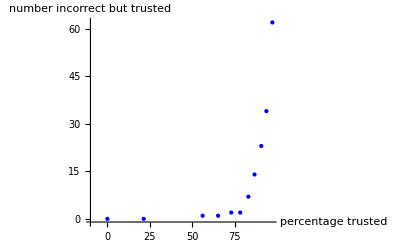

```mathematica
ListPlot[paretoFront,AxesLabel->{"percentage trusted","number incorrect but trusted"},AxesOrigin->{-10,-1},PlotStyle->{PointSize[Medium],Blue}]
```

### Confusion matrix

```mathematica
ensembleConfusionData=Transpose[Map[Thread[{testValues,#}]&,Map[First[Ordering[#,1,Greater]-1]&,Map[(vars/.bestweights).#&,allVals],{-2}],{1}],{2,1}];
Dimensions[ensembleConfusionData]
mergedEnsmbleConfusionData=Apply[Join,ensembleConfusionData];
Dimensions[mergedEnsmbleConfusionData]
ensembleTallies=Apply[Rule[#1+1,#2]&,Tally[mergedEnsmbleConfusionData],{1}];
confusionmatrix=Normal[SparseArray[ensembleTallies]]
```

{119,40,2}

{4760,2}

{{830,0,10,0},{0,1262,18,0},{3,37,1262,18},{1,0,5,1314}}

```mathematica
tg=Labeled[TextGrid[Prepend[Join[Transpose@{Range[0,3]},confusionmatrix,2],Prepend[Range[0,3],""]],Frame->All,Dividers->{{{Thickness[2],Thickness[2],True,True,True}},{{Thickness[2],Thickness[2],True,True,True}}},Background->{1->White,{1->White},Join[{{{2,-1},{2,-1}}->LightRed},Thread[Map[{#,#}&,Range[2,5]]->Green]]}],{"expected","actual","confusion matrix"},{Left,Top,Bottom}]
```

| 0 | 1 | 2 | 3
0 | 830 | 0 | 10 | 0
1 | 0 | 1262 | 18 | 0
2 | 3 | 37 | 1262 | 18
3 | 1 | 0 | 5 | 1314expectedactualconfusion matrix

### Apply the optimal weights to each of the 40 individual trials

We show the number of misses, and correctness percentage, for each of the 40 trials, as assessed using the best set of weights. We then give the range, mean, and median of this set of correct percentages.

```mathematica
totaledValues=Map[(vars/.bestweights).#&,allVals];
bestvals=Map[First[Ordering[#,1,Greater]-1]&,totaledValues,{2}];
diffs=Map[#-testValues&,bestvals,{1}];
misses=Map[Total,Clip[Abs[diffs]],{1}];
correctPercentages=(119-misses)/119.;
Transpose[{misses,correctPercentages}]
{MinMax[correctPercentages],Mean[correctPercentages],Median[correctPercentages]}
```

{{1,0.991597},{1,0.991597},{3,0.97479},{2,0.983193},{1,0.991597},{3,0.97479},{3,0.97479},{3,0.97479},{3,0.97479},{1,0.991597},{2,0.983193},{2,0.983193},{3,0.97479},{0,1.},{2,0.983193},{2,0.983193},{2,0.983193},{2,0.983193},{0,1.},{1,0.991597},{2,0.983193},{3,0.97479},{2,0.983193},{4,0.966387},{3,0.97479},{1,0.991597},{2,0.983193},{2,0.983193},{2,0.983193},{1,0.991597},{2,0.983193},{1,0.991597},{4,0.966387},{5,0.957983},{4,0.966387},{2,0.983193},{2,0.983193},{7,0.941176},{3,0.97479},{3,0.97479}}

{{0.941176,1.},0.980672,0.983193}

Perhaps notable is that even the worst trial still came to 94% correct.

### Other things attempted

I tried to forego optimizing weights, instead using reciprocals of individual method success rates (as measured over the 40 trials). Variant: use some power of those reciprocals (helps to separate them better).
Also used this in tandem with raising probabilities to some power, such as 2. The idea here is to better emphasize results that seem “certain” over those that are guessing lower probabilities.
Upshot: I found no combination of these that gave better than a 97% success rate overall. So the DE-based weight computation seems to be important.

### Correlations between methods

```mathematica
allVals=Import["all_values.m"];
tvals=Transpose[allVals,{2,1}];
Dimensions[tvals]
tjvals=Apply[Join,tvals,{1}];
Dimensions[tjvals]
```

{7,40,119,4}

{7,4760,4}

```mathematica
correlations=Table[{i,j,Correlation[tjvals[[i]],tjvals[[j]]]},{i,Length[tjvals]},{j,i}]
```

{{{1,1,{{1.,-0.238682,-0.49282,-0.501303},{-0.238682,1.,0.268814,-0.509153},{-0.49282,0.268814,1.,-0.345108},{-0.501303,-0.509153,-0.345108,1.}}}},{{2,1,{{0.924891,-0.337499,-0.448824,-0.403034},{-0.13191,0.80536,-0.00292208,-0.321166},{-0.325551,0.113098,0.815526,-0.295786},{-0.390375,-0.517327,-0.358733,0.906639}}},{2,2,{{1.,-0.275706,-0.334846,-0.32102},{-0.275706,1.,-0.260634,-0.39719},{-0.334846,-0.260634,1.,-0.402094},{-0.32102,-0.39719,-0.402094,1.}}}},{{3,1,{{0.923244,-0.354218,-0.452343,-0.389734},{-0.128308,0.820458,-0.0160603,-0.324279},{-0.307289,0.0280824,0.812884,-0.264091},{-0.374227,-0.532191,-0.378079,0.912336}}},{3,2,{{0.968411,-0.279512,-0.317707,-0.305944},{-0.270928,0.898851,-0.184611,-0.382697},{-0.281242,-0.268505,0.874473,-0.326068},{-0.2974,-0.387899,-0.38724,0.957527}}},{3,3,{{1.,-0.296322,-0.293021,-0.288218},{-0.296322,1.,-0.346263,-0.398302},{-0.293021,-0.346263,1.,-0.369945},{-0.288218,-0.398302,-0.369945,1.}}}},{{4,1,{{0.929897,-0.347688,-0.453468,-0.399054},{-0.137087,0.821907,-0.00337528,-0.32512},{-0.315291,0.03387,0.820127,-0.26446},{-0.38295,-0.525827,-0.374068,0.914508}}},{4,2,{{0.974051,-0.275452,-0.319173,-0.313076},{-0.274843,0.912009,-0.186123,-0.389443},{-0.29267,-0.269082,0.889503,-0.329467},{-0.309175,-0.390562,-0.379614,0.963096}}},{4,3,{{0.980435,-0.281927,-0.284534,-0.293739},{-0.289527,0.959182,-0.314691,-0.3943},{-0.296843,-0.307594,0.950984,-0.357549},{-0.296563,-0.39435,-0.343114,0.9774}}},{4,4,{{1.,-0.293674,-0.299681,-0.306977},{-0.293674,1.,-0.330275,-0.402296},{-0.299681,-0.330275,1.,-0.360995},{-0.306977,-0.402296,-0.360995,1.}}}},{{5,1,{{0.919176,-0.347017,-0.450195,-0.391276},{-0.136009,0.798327,0.00912564,-0.321353},{-0.300065,0.0242783,0.783704,-0.249373},{-0.375482,-0.513842,-0.368701,0.896998}}},{5,2,{{0.959027,-0.276844,-0.311008,-0.306285},{-0.269224,0.873135,-0.164409,-0.380247},{-0.275989,-0.253427,0.841467,-0.313425},{-0.301001,-0.38305,-0.372688,0.942976}}},{5,3,{{0.964513,-0.277836,-0.279831,-0.288565},{-0.278963,0.917952,-0.285479,-0.390869},{-0.28051,-0.294684,0.902705,-0.337813},{-0.291773,-0.387136,-0.338303,0.961483}}},{5,4,{{0.978644,-0.292255,-0.290141,-0.298673},{-0.281505,0.943977,-0.298666,-0.388382},{-0.283315,-0.303776,0.931652,-0.336532},{-0.298829,-0.391729,-0.343992,0.96656}}},{5,5,{{1.,-0.296797,-0.288821,-0.296925},{-0.296797,1.,-0.348848,-0.400195},{-0.288821,-0.348848,1.,-0.360806},{-0.296925,-0.400195,-0.360806,1.}}}},{{6,1,{{0.923956,-0.351283,-0.460358,-0.386689},{-0.11493,0.755634,-0.0133065,-0.302781},{-0.292162,0.0455687,0.750844,-0.246879},{-0.37079,-0.502291,-0.365542,0.883891}}},{6,2,{{0.96486,-0.276762,-0.320992,-0.302229},{-0.252472,0.821314,-0.168056,-0.345979},{-0.262318,-0.228549,0.763951,-0.275645},{-0.298899,-0.350046,-0.342978,0.884733}}},{6,3,{{0.971551,-0.2807,-0.29113,-0.280906},{-0.26748,0.861401,-0.280019,-0.350154},{-0.272561,-0.269465,0.816905,-0.286777},{-0.279104,-0.344744,-0.310928,0.882196}}},{6,4,{{0.973938,-0.288478,-0.295461,-0.293201},{-0.262446,0.877835,-0.277863,-0.36047},{-0.268451,-0.265685,0.809203,-0.270941},{-0.290369,-0.358412,-0.301501,0.886698}}},{6,5,{{0.958097,-0.281275,-0.277693,-0.286611},{-0.27113,0.848346,-0.270891,-0.346704},{-0.25391,-0.248372,0.776988,-0.277234},{-0.283156,-0.35286,-0.29052,0.873815}}},{6,6,{{1.,-0.275096,-0.292486,-0.275243},{-0.275096,1.,-0.387554,-0.366714},{-0.292486,-0.387554,1.,-0.39023},{-0.275243,-0.366714,-0.39023,1.}}}},{{7,1,{{0.850583,-0.327553,-0.36208,-0.39503},{-0.168829,0.763897,0.117917,-0.343355},{-0.220606,0.0583055,0.658526,-0.261175},{-0.337466,-0.523445,-0.366465,0.864177}}},{7,2,{{0.884181,-0.278188,-0.216659,-0.326912},{-0.286855,0.798326,-0.0402857,-0.41374},{-0.215441,-0.182897,0.734847,-0.329764},{-0.254631,-0.397419,-0.393214,0.934097}}},{7,3,{{0.89569,-0.286051,-0.188593,-0.309062},{-0.306119,0.809806,-0.122248,-0.41808},{-0.208215,-0.186989,0.732878,-0.342792},{-0.251209,-0.398828,-0.334905,0.934712}}},{7,4,{{0.896143,-0.292575,-0.191713,-0.319082},{-0.30887,0.827057,-0.119176,-0.42033},{-0.206081,-0.189995,0.741783,-0.335374},{-0.250674,-0.407784,-0.342714,0.938808}}},{7,5,{{0.877988,-0.279613,-0.180459,-0.311834},{-0.309408,0.796418,-0.119731,-0.40671},{-0.189388,-0.183289,0.710106,-0.333739},{-0.249353,-0.394108,-0.325086,0.918482}}},{7,6,{{0.898308,-0.267818,-0.197628,-0.293374},{-0.302826,0.738193,-0.0927322,-0.384234},{-0.218501,-0.175421,0.629965,-0.285313},{-0.248009,-0.353794,-0.271309,0.842014}}},{7,7,{{1.,-0.340346,-0.20147,-0.307398},{-0.340346,1.,-0.290716,-0.453517},{-0.20147,-0.290716,1.,-0.382056},{-0.307398,-0.453517,-0.382056,1.}}}}}

Now we flatten and check correlations.

```mathematica
tjfvals=Map[Flatten,tvals];
Dimensions[tjfvals]
```

{7,19040}

```mathematica
correlations=Table[{i,j,Correlation[tjfvals[[i]],tjfvals[[j]]]},{i,Length[tjvals]},{j,i}]
```

{{{1,1,1.}},{{2,1,0.848387},{2,2,1.}},{{3,1,0.830111},{3,2,0.922435},{3,3,1.}},{{4,1,0.839355},{4,2,0.933436},{4,3,0.966634},{4,4,1.}},{{5,1,0.814756},{5,2,0.901462},{5,3,0.935956},{5,4,0.954609},{5,5,1.}},{{6,1,0.795553},{6,2,0.853049},{6,3,0.877646},{6,4,0.881697},{6,5,0.858194},{6,6,1.}},{{7,1,0.756555},{7,2,0.837047},{7,3,0.843972},{7,4,0.852895},{7,5,0.828161},{7,6,0.769191},{7,7,1.}}}

#### Cohen Kappa correlation (unweighted)

Here we show the Cohen Kappa correlation values for all pairs of methods.

```mathematica
totaledValues=Map[(vars/.naiveweights).#&,allVals];
bestvals7=Map[First[Ordering[#,1,Greater]-1]&,allVals,{3}];
```

```mathematica
bestvalsLists=Transpose[Flatten[Transpose[bestvals7,{1,3,2}],1]];
Dimensions[bestvalsLists]
```

{7,4760}

```mathematica
cohenKappa[l1_,l2_,rng_]:=Module[
{tallies=Tally[Transpose[{l1,l2}]],tally1Vec,tally2Vec,len=Length[l1],agreed,pObs,pEmp},
agreed=Total[Cases[tallies,{{a_,a_},b_}:>b]];
pObs=agreed/len;
tally1Vec=SparseArray[Map[#[[1]]+1-rng[[1]]->#[[2]]&,Tally[l1]],Length[rng]];
tally2Vec=SparseArray[Map[#[[1]]+1-rng[[1]]->#[[2]]&,Tally[l2]],Length[rng]];
pEmp=tally1Vec.tally2Vec/len^2;
(pObs-pEmp)/(1-pEmp)
]
```

```mathematica
cohenKappaTable=Table[{i,j,cohenKappa[bestvalsLists[[i]],bestvalsLists[[j]],Range[0,3]]},{i,Length[bestvalsLists]},{j,i}];
N[cohenKappaTable]
```

{{{1.,1.,1.}},{{2.,1.,0.822805},{2.,2.,1.}},{{3.,1.,0.839903},{3.,2.,0.852393},{3.,3.,1.}},{{4.,1.,0.849507},{4.,2.,0.868212},{4.,3.,0.932983},{4.,4.,1.}},{{5.,1.,0.827597},{5.,2.,0.836688},{5.,3.,0.894502},{5.,4.,0.919752},{5.,5.,1.}},{{6.,1.,0.828208},{6.,2.,0.806431},{6.,3.,0.850498},{6.,4.,0.854057},{6.,5.,0.834027},{6.,6.,1.}},{{7.,1.,0.728087},{7.,2.,0.765689},{7.,3.,0.793001},{7.,4.,0.807426},{7.,5.,0.781996},{7.,6.,0.737987},{7.,7.,1.}}}